```mathematica
(* This cell is basically housekeeping and setup stuff; it can be ignored *)
ClearAll["Global`*"];ParamsAreSet=False;
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];
AutoLoadDir=SetDirectory["./Mathematica/CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;
```

Solving ...

Below 𝓂MinPermitted after 63 backwards Euler iterations.

Last 2 Points:(0.824412 | 0.342591 | 0.330215 | -21.6355 | -0.203069
-0.0283241 | 0.143006 | -2.10391 | -19.4339 | -81.0262)

Solving ...

Above 𝓂MaxPermitted after 119 backwards Euler iterations.

Last 2 Points:(97.6944 | 7.47043 | 0.062828 | -2.17971 | -0.0000302828
102.097 | 7.74672 | 0.0627009 | -2.10364 | -0.0000275432)

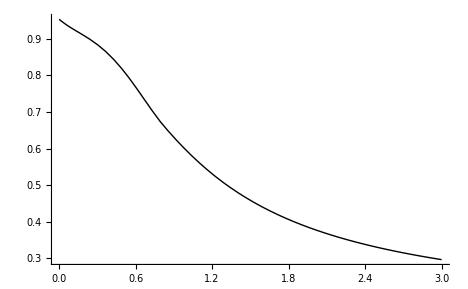

```mathematica
Print[Show[RiskAversionOfTheValueFunctionBase = Plot[ρ cE'[m],{m,0,3}]]];
```

```mathematica
ρ=4;
FindStableArm;
```

Solving ...

Below 𝓂MinPermitted after 170 backwards Euler iterations.

Last 2 Points:(2.1393 | 0.295346 | 0.119673 | -124.378 | -0.0160272
1.30049 | 0.188809 | 0.13487 | -407.466 | -0.0195926)

Solving ...

Above 𝓂MaxPermitted after 239 backwards Euler iterations.

Last 2 Points:(99.5088 | 5.6254 | 0.0471118 | -0.0404152 | -0.0000298402
101.856 | 5.73591 | 0.0470436 | -0.0381604 | -0.0000283478)

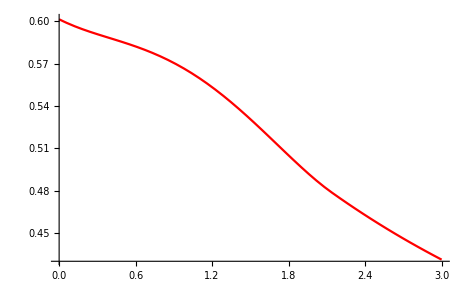

```mathematica
Print[Show[RiskAversionOfTheValueFunctionHiRho = Plot[ρ cE'[m],{m,0,3},PlotStyle->{Red}]]];
```

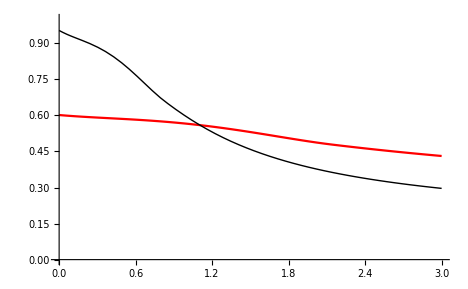

```mathematica
Print[RiskAversionOfTheValueFunctionRhoLoAndHi = Show[RiskAversionOfTheValueFunctionHiRho,RiskAversionOfTheValueFunctionBase,PlotRange->{{0,3},{0,1.}},AxesOrigin->{0.,0.}]];
```